```mathematica
params={g1,g2,g3,gp1,gp2,gp3,J12,J23,J12p,J23p,jss1,dJ12,dJ23};

aspts=Element[params,Reals]&&And@@Thread[params>0];

$Assumptions=aspts; (*assume everything is real and positive*)
(*note that I introduce factors of 2 here already so no 1/4 in the exchanges*)
sx=PauliMatrix[1]/2;
sy=PauliMatrix[2]/2;
sz=PauliMatrix[3]/2;
id=IdentityMatrix[2];

decompose[M_]:=(Tr[M.#])&/@svec;
pauli1[i_,n_,m_]:=KroneckerProduct@@ReplacePart[ConstantArray[id,m],n->svec[[i]]];
Sztot[n_]:=Total@Table[pauli1[3,k,n],{k,1,n}]; (*3q total Sz operator*)
svec={sx,sy,sz};
pauli2[i_,j_,n_,l_,m_]:=KroneckerProduct@@ReplacePart[ConstantArray[id,m],{n->svec[[i]],l->svec[[j]]}];
(* i-th pauli for n-th spin, j-th pauli for l-th spin*)
gfactors1={g1,g2,g3};
gfactors2={gp1,gp2,gp3};
J1={J12,J23};
J2={J12p,J23p}; (*the second qubit*)
exch1=J12*Total@Table[pauli2[i,i,1,2,3],{i,3}]+J23*Total@Table[pauli2[i,i,2,3,3],{i,3}];
H1=gfactors1.Table[pauli1[3,k,3],{k,3}]+exch1; (*qubit 1 ham*)
H2=gfactors2.Table[pauli1[3,k,3],{k,3}]+J12p*Total@Table[pauli2[i,i,1,2,3],{i,3}]+J23p*Total@Table[pauli2[i,i,2,3,3],{i,3}]; (*qubit 2 ham*)

sumPauli[a_,b_]:=Sum[KroneckerProduct[pauli1[i,a,3],pauli1[i,b,3]],{i,3}];
pairs={
{3,3},(*Jss1*)
{3,2},(*Jsc*)
{3,1},(*Jss2*)
{1,1},(*Jss3*)
{1,2},(*Jss4*)
{2,2},(*Jss5*)
{1,3},(*Jss6*)
{2,1},(*Jss7*)
{2,3}  (*Jss8*)};


coeffs={jss1,jsc,jss2,jss3,jss4,jss5,jss6,jss7,jss8};

{Jss1,Jsc,Jss2,Jss3,Jss4,Jss5,Jss6,Jss7,Jss8}=coeffs*(sumPauli@@@pairs);
(*introduce all the possible exchanges between the 2 qubits*)
Jint=Total@{Jss1,Jsc,Jss2,Jss3,Jss4,Jss5,Jss6,Jss7,Jss8};
norm=#1/Sqrt[#1.#1]&;
```

```mathematica
dim=8;
basis=IdentityMatrix[8];
Sztot3=Sztot[3];
mzvals=Table[Conjugate[basis[[All,k]]].(Sztot3.basis[[All,k]]),{k,dim}];  (*enumerate the  zeeman basis states by their mz projections*)
mMinusIndices=Flatten@Position[mzvals,-1/2];
projMinus=basis[[All,mMinusIndices]]; (*take only the states with mz=-1/2*)
H1minus23=ConjugateTranspose[projMinus].H1.projMinus;
H1minus=ConjugateTranspose[projMinus].H1.projMinus /.J23->0  (*1 q ham in this subspace*)
{evalsH1minus,evecsH1minus}=Eigensystem[H1minus]//FullSimplify

ElogH10=evalsH1minus[[1]];
ElogH11=evalsH1minus[[2]];

(ElogH10-ElogH11)//FullSimplify;
j12idle=Solve[1/2 (-g1-g2+2 g3+J12+√((g1-g2)^2+J12^2))==0,J12]//FullSimplify  (*here i find the idle point*)
ruleJ12=First@(j12idle/. {J12->ConditionalExpression[expr_,_]}:>(J12->expr));

condJ12=First@(j12idle/. {J12->ConditionalExpression[_,cond_]}:>cond);
{ruleJ12p,condJ12p}={ruleJ12,condJ12}/.Join[Table[Symbol["g"<>ToString[i]]->Symbol["gp"<>ToString[i]],{i,3}],{J12->J12p}];
Clear[dJ12,dJ23]; (*just a fucked up way to create the same rules for the idle point but for the other qubit*)


$Assumptions=Element[params,Reals]&&And@@Thread[params>0]&&condJ12&&condJ12p&&dJ23>0; (*adding assumptions for the idle point to the global assumptions*)
(*
H1idle=Simplify[H1/. ruleJ12/. J23->0];
H2idle=H1idle /.Thread[gfactors1 ->gfactors2]//FullSimplify;

*)
```

{{g1/2-g2/2-g3/2-J12/4,J12/2,0},{J12/2,-g1/2+g2/2-g3/2-J12/4,0},{0,0,-g1/2-g2/2+g3/2+J12/4}}

{{1/4 (-2 (g1+g2-g3)+J12),1/4 (-2 g3-J12-2 √((g1-g2)^2+J12^2)),1/4 (-2 g3-J12+2 √((g1-g2)^2+J12^2))},{{0,0,1},{-(-g1+g2+√((g1-g2)^2+J12^2))/J12,1,0},{(g1-g2+√((g1-g2)^2+J12^2))/J12,1,0}}}

{{J12→ConditionalExpression[(2 (g1-g3) (g2-g3))/(g1+g2-2 g3), g2>g3&&g1>g3]}}

```mathematica
Hidle=H1minus/.ruleJ12/.J23->0//Simplify; (*get single q idle and the eigenbasis*)
vecs=Eigenvectors[H1minus]/.ruleJ12/.J23->0//Simplify;
vecs=norm/@vecs;
ConjugateTranspose[projMinus].(gfactors1.Table[pauli1[3,k,3],{k,3}]).projMinus; (*this i need just to see who is who in the 0-1 basis in terms of the zeeman basis*)
```

```mathematica
dH=Conjugate[vecs[[1;;2]]].(H1minus23-Hidle).Transpose[vecs[[1;;2]]]/.J23->dJ23/.J12->(ruleJ12[[2]])+dJ12 //Simplify; (*finding the deviation from the idle point*)
decompose[dH]//FullSimplify (*decompose the tangent ham in terms of the sigmax sigmay sigmaz*)
Evaluate[decompose[dH]/.dJ12->(dJ+sJ)/2/.dJ23->(sJ-dJ)/2/.Thread[gfactors1->{56,75,47}]]//N//Simplify (*compare numbers to the xoso code*)
```

{dJ23/(2 √(1+(g2-g3)^2/(g1-g3)^2)),0,(dJ12 (g1+g2-2 g3)^2-dJ23 (g2-g3)^2)/(4 (g1^2+g2^2-2 (g1+g2) g3+2 g3^2))}

{0.0765023 (-1. dJ+sJ),0.,0.+0.311127 dJ+0.0845376 sJ}

```mathematica
{dJ23/(2 √(1+(g2-g3)^2/(g1-g3)^2)),0,(dJ12 (g1+g2-2 g3)^2-dJ23 (g2-g3)^2)/(4 (g1^2+g2^2-2 (g1+g2) g3+2 g3^2))}
ruleJ12[[2]]/.Thread[gfactors1->{56,75,47}]//N
```

{dJ23/(2 √(1+(g2-g3)^2/(g1-g3)^2)),0,(dJ12 (g1+g2-2 g3)^2-dJ23 (g2-g3)^2)/(4 (g1^2+g2^2-2 (g1+g2) g3+2 g3^2))}

13.6216

```mathematica
Clear[mA,mB]

{vals1,vecs1}=Eigensystem[H1 /.J23->0] //FullSimplify;
{vals2,vecs2}={vals1,vecs1}/.Thread[gfactors1->gfactors2]/.J12->J12p;
normalize[v_]:=v/Sqrt[Conjugate[v].Transpose[v]];
vecs={vecs1,vecs2}=(normalize/@#//FullSimplify)&/@{vecs1,vecs2};

{mA,mB}=Table[Simplify[Conjugate[#[[k]]].(Sztot3.Transpose[#[[k]]])],{k,dim}]&/@vecs;
(*diagonalize both 1q hams separately and enumerate the eigenstates by their mz*)
```

```mathematica
twoQData=Table[Module[{EA=vals1[[i]],EB=vals2[[j]],mTot,psi},mTot=mA[[i]]+mB[[j]];
psi=KroneckerProduct[vecs1[[i]],vecs2[[j]]]; 
{i,j,EA+EB,mTot,psi}],{i,dim},{j,dim}];
(*{iA,jB,Eij,MzTot,psi_ij}*)

(*select only M_z=-1 out of all the 2q states*)


twoQMzMinus1Raw=Cases[twoQData,{i_,j_,E_,mz_,psi_}/;Simplify[mz==-1],{2}];

twoQMzMinus1=twoQMzMinus1Raw/. ruleJ12/. ruleJ12p;
eps=-10^(-3); (*i don't want the logical space to be perfectly degenerate*)
epsp=-0.5*10^(-3);
ruleJ12eps={J12->ruleJ12[[2]]+eps};
ruleJ12peps={J12p->ruleJ12p[[2]]+epsp};
Clear[ElogH20];
ElogH20=Simplify[ElogH10/.{J12->J12p}/. Thread[gfactors1->gfactors2] ]/.ruleJ12peps;
ElogH21=Simplify[ElogH11/.{J12->J12p}/.Thread[gfactors1->gfactors2]]/.ruleJ12peps;
E00=Simplify[ElogH10+ElogH20/.ruleJ12eps]; (*logical space eigenenergies*)
E01=Simplify[ElogH10+ElogH21/.ruleJ12eps];
E10=Simplify[ElogH11+ElogH20/.ruleJ12eps];
E11=Simplify[ElogH11+ElogH21/.ruleJ12eps];
```

```mathematica
g1t={g1->56,g2->75,g3->47(*MHz*)

};
g2t={gp1->60,gp2->72,gp3->43(*MHz*)

}; (*copypast params from the xoso*)
(*pars1={
θ1->0.01,θ2->0.01,
g1->60,g2->74,g3->47(*MHz*)
(*J->1*)
};
pars2={
θ1->0.01,θ2->0.01,
g1->62,g2->72,g3->43(*MHz*)
(*J->1*)*)
(*sort the eigenstates by energies within the m_z=-1 subspace substituting these specific g factors by their energy proximity to the logical states*)
Closeststate[Etarget_]:=Sort[twoQMzMinus1Raw/. ruleJ12eps/. ruleJ12peps/.g1t/.g2t,Simplify[Abs[#1[[3]]-Etarget]>Abs[#2[[3]]-Etarget]]&];
Emin=Min[{E00,E01,E10,E11}/.g1t/.g2t];
ordered=Closeststate[Emin]//FullSimplify;
```

```mathematica
orderedpairs=ordered[[All,{1,2}]];

Clear[GetStateByIndices];GetStateByIndices[{iA_,jB_}]:=FirstCase[twoQMzMinus1,{iA,jB,El_,mz_,psi_}:>{El,psi},{1}];

AnalyticalStates=GetStateByIndices/@orderedpairs;
SortedAnalyticalEnergies=AnalyticalStates[[All,1]];
SortedAnalyticalWaveFunctions=AnalyticalStates[[All,2]];
```

```mathematica
Abs[#-SortedAnalyticalEnergies[[-1]]]&/@SortedAnalyticalEnergies /.g1t/.g2t//N  (*energies of the closest states*)
```

{47.9436,42.,41.,27.3784,24.5652,24.5652,23.3784,23.3784,20.5652,4.,4.,0.,0.,0.,0.}

```mathematica
wfs=Flatten/@SortedAnalyticalWaveFunctions[[-6;;-5]]//Simplify; (*leakage subspace*)
l1=Flatten/@SortedAnalyticalWaveFunctions[[-4;;-1]]; (*logical subspace*)
wfs.KroneckerProduct[Sztot[3],IdentityMatrix[8]].Transpose[wfs]//Simplify//MatrixForm (*what are the mzs of the leakage states at each qubit*)
wfs.KroneckerProduct[IdentityMatrix[8],Sztot[3]].Transpose[wfs]//Simplify//MatrixForm
```

(1/2 | 0
0 | -3/2)

(-3/2 | 0
0 | 1/2)

```mathematica
totJ=wfs.Jint.Transpose[l1]/.g1t/.g2t//Simplify; (*just a naive way to find a combo of exchanges between the two qubits such that the coupling betweent he logical and leakage space is 0*)
Solve[totJ==0,{jsc,jss1,jss2,jss3,jss4,jss5,jss7,jss8}]
```

{}

```mathematica
FullSimplify[Abs[SortedAnalyticalEnergies[[-5]]-SortedAnalyticalEnergies[[-1]]],Assumptions->gp1+gp2-2 gp3>0]
FullSimplify[Abs[SortedAnalyticalEnergies[[-6]]-SortedAnalyticalEnergies[[-1]]],Assumptions->g1+g2-2*g3>0 ]
(*gaps to the leakage states*)
```

Abs[g3-gp3]

Abs[g3-gp3]

```mathematica
Clear[dJ12,dJ23];
exprJ12idle=J12/. ruleJ12;   
exprJ12pidle=J12p/. ruleJ12p;  
H1idle=H1/. {J12->exprJ12idle,J23->0} /.g1t;
H2idle=H2/. {J12p->exprJ12pidle,J23p->0} /.g2t;
Htotidle=(KroneckerProduct[H1idle,IdentityMatrix[8]]+KroneckerProduct[IdentityMatrix[8],H2idle]); (*1q and 2q idle hams*)
```

```mathematica
logandleak=Flatten/@SortedAnalyticalWaveFunctions[[-6;;-1]]//Simplify;
Hintfull=logandleak.Jss1.Transpose[logandleak]//FullSimplify;
Htotidleproj=logandleak.Htotidle.Transpose[logandleak]/.g1t/.g2t//Simplify;
UCZfull[t_]:=MatrixExp[-I*Hintfull*t-I*Htotidleproj*t]//FullSimplify; (*find evolution when the exchange between the 3rd and 3rd spin is on, with the total idle ham and the additional exchange ham*)
UCZfull[t][[1;;2,3;;6]]//MatrixForm (*see how it couples the leakage and logical subspace*)
```

(0 | -(ⅇ^((ⅈ (257805+851 jss1-1702 √(16+jss1^2)) t)/3404) (-1+ⅇ^(ⅈ √(16+jss1^2) t)) jss1)/(2 √(16+jss1^2)) | 0 | 0
0 | 0 | -(ⅇ^((ⅈ (271421+851 jss1-1702 √(16+jss1^2)) t)/3404) (-1+ⅇ^(ⅈ √(16+jss1^2) t)) jss1)/(2 √(16+jss1^2)) | 0)

```mathematica
H1shift=H1/. {J12->exprJ12idle+dJ12,J23->0+dJ23};
H1lin=Normal@Series[H1shift,{dJ12,0,1},{dJ23,0,1}]//Simplify;
H1linproj=logandleak.KroneckerProduct[H1lin,IdentityMatrix[8]].Transpose[logandleak]//Simplify;
Hdj120=H1linproj/.dJ12->0/.g1t//Simplify;
```

```mathematica
(*U1q[t_]:=MatrixExp[-I*t*Hdj120]//Simplify;
UCZred=UCZfull[Pi/jss1]//Simplify;
Utot[t2_]:=UCZred.U1q[t2].UCZred;
L[t2_]:=Utot[t2]//Simplify
Clear[t2];
L[t2][[1;;2,3;;6]]//MatrixForm
L[t2][[3;;6,3;;6]]//MatrixForm*)
```

(0 | 0 | 0 | 9/946 ⅈ √865 ⅇ^(-1/148 ⅈ (-5712+37 dJ23) t2) (-1+ⅇ^((473 ⅈ dJ23 t2)/865))
9/946 ⅈ √865 ⅇ^(-1/148 ⅈ (-5712+37 dJ23) t2) (-1+ⅇ^((473 ⅈ dJ23 t2)/865)) | 0 | 0 | 0)

(-1/946 ⅈ ⅇ^(-1/148 ⅈ (-5712+37 dJ23) t2) (865+81 ⅇ^((473 ⅈ dJ23 t2)/865)) | 0 | 0 | 0
0 | -ⅈ ⅇ^((-(311 ⅈ)/37+(703 ⅈ dJ23)/3460) t2) | 0 | 0
0 | 0 | -ⅈ ⅇ^(1/148 ⅈ (12668-37 dJ23) t2) | 0
0 | 0 | 0 | -1/946 ⅈ ⅇ^(-1/148 ⅈ (-5712+37 dJ23) t2) (81+865 ⅇ^((473 ⅈ dJ23 t2)/865)))

```mathematica
(*Clear[t2];

sub=L[t2][[1;;2,3;;6]];        

eqs=Thread[Flatten[sub]==0];  
red=Reduce[eqs,t2];     

sol1=First@Solve[{red,C[1]==-1},{t2,C[1]}];

t2min=t2/. sol1      *)
sub=UCZfull[t2][[1;;2,3;;6]];        

eqs=Thread[Flatten[sub]==0];  
red=Reduce[eqs,t2];     

sol1=First@Solve[{red,C[1]==1},{t2,C[1]}];

t2min=(t2/. sol1)[[1]] (*find such timing that the leakage is 0*)
```

(2 π)/(√(16+jss1^2))

```mathematica
(*Uideal=Utot[t2min][[3;;6,3;;6]]//Simplify//MatrixForm
diag=Diagonal[Uideal//First]; (*{λ11,λ10,λ01,λ00}*)

Simplify[diag[[1]] diag[[4]]/(diag[[2]] diag[[3]])]*)
```

```mathematica
diagfull=Diagonal[UCZfull[t2min][[3;;6,3;;6]]]//FullSimplify (*find the resulting gate in the logical space*)
```

{ⅇ^((ⅈ (264613-851 jss1) π)/(1702 √(16+jss1^2))),-ⅇ^((ⅈ (257805+851 jss1) π)/(1702 √(16+jss1^2))),-ⅇ^((ⅈ (271421+851 jss1) π)/(1702 √(16+jss1^2))),ⅇ^((ⅈ (264613-851 jss1) π)/(1702 √(16+jss1^2)))}

```mathematica
Simplify[(diagfull[[1]] diagfull[[4]])/(diagfull[[2]] diagfull[[3]])] (*stupid way to check that it's not just a product of 2 single qubit phase gates*)
```

ⅇ^(-(2 ⅈ jss1 π)/(√(16+jss1^2)))

```mathematica
UCZfull[t2min][[3;;6,3;;6]]
```

{{ⅇ^((ⅈ (264613-851 jss1) π)/(1702 √(16+jss1^2))),0,0,0},{0,-ⅇ^((ⅈ (257805+851 jss1) π)/(1702 √(16+jss1^2))),0,0},{0,0,-ⅇ^((ⅈ (271421+851 jss1) π)/(1702 √(16+jss1^2))),0},{0,0,0,ⅇ^((ⅈ (264613-851 jss1) π)/(1702 √(16+jss1^2)))}}

```mathematica
Hex=H1minus/.{g1->56,g2->75,g3->47};
```

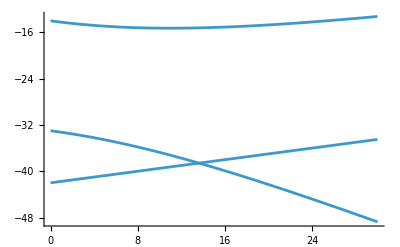

```mathematica
Plot[Sort[Eigenvalues[Hex]],{J12,0,30}] (*plot for the states in the mz=-1/2 subspace as the function of the 12 exchange*)
```

```mathematica
condJ12
```

g2>g3&&g1>g3

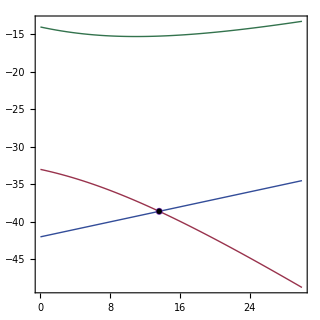

```mathematica
Needs["MaTeX`"];

SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath}","\\usepackage{lmodern}"}];
tex[s_,fs_:20]:=MaTeX[s,FontSize->fs];

niceColors={RGBColor[0.20,0.30,0.60],RGBColor[0.60,0.20,0.30],RGBColor[0.20,0.45,0.30],RGBColor[0.45,0.35,0.15],RGBColor[0.35,0.35,0.35],RGBColor[0.25,0.40,0.50]};

vals=Sort[Eigenvalues[Hex]];
cols=Take[niceColors,UpTo[Length[vals]]];

jid=13.6216;
evAtIdle=Sort@Eigenvalues[Hex/. J12->jid];
Eidle=Mean@evAtIdle[[{1,2}]];  (*center between the two lowest levels*)

purple=RGBColor[0.45,0.20,0.70];

p=Plot[Evaluate[vals],{J12,0,30},PlotRange->All,PlotStyle->(Directive[Thick,#]&/@cols),Frame->True,FrameStyle->Black,FrameTicksStyle->Directive[Black,FontFamily->"Times",16],(*TicksStyle->Directive[Black,FontFamily->"Times",18],*)FrameLabel->{tex["J_{12}/h, \ \ \\text{MHz}",18],tex["\\text{eigenenergies, MHz}",18]},PlotLabel->tex["S_z^{\\text{total}}=-\\frac{1}{2}\\ \\text{subspace}",18],GridLines->None,AspectRatio->1,ImageSize->320,ImagePadding->{{60,15},{50,20}},PlotRangeClipping->False,Epilog->{Inset[Graphics[{Directive[purple,Thick],Circle[{0,0},1]}],{jid,Eidle},Center,Scaled[0.08]],Inset[tex["\\text{idle point}",18],Offset[{35,25},{jid,Eidle}]]}]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Downloads","spectrum_SzminusHalf.pdf"}],p]
```

C:\Users\tesya\Downloads\spectrum_SzminusHalf.pdf

1q gates

```mathematica
(*sigmaz*)
hz=(dJ12 (g1+g2-2 g3)^2)/(4 (g1^2+g2^2-2 (g1+g2) g3+2 g3^2))*PauliMatrix[3]/.g1t;
Uz[t_]:=MatrixExp[-I*hz*t]//FullSimplify
soltarz=First@Solve[hz[[1,1]]*t==Pi/2,t];
Uztarget=Uz[t]/.soltarz
tztarget=soltarz[[1,2]]
```

{{-ⅈ,0},{0,ⅈ}}

(1730 π)/(1369 dJ12)

```mathematica
(*sigmax*)
solJ12=Solve[(dJ12 (g1+g2-2 g3)^2-dJ23 (g2-g3)^2)/(4 (g1^2+g2^2-2 (g1+g2) g3+2 g3^2))==0/.g1t,dJ12][[1,1,2,1]]
hx=(dJ23*PauliMatrix[1])/(2 √(1+(g2-g3)^2/(g1-g3)^2))/.g1t;
Ux[t_]:=MatrixExp[-I*hx*t]//FullSimplify
soltarx=First@Solve[hx[[1,2]]*t==Pi/2,t];
Uxtarget=Ux[t]/.soltarx
txtarget=soltarx[[1,2]]
```

(784 dJ23)/1369

{{0,-ⅈ},{-ⅈ,0}}

(√865 π)/(9 dJ23)